```mathematica
Exit[]
```

```mathematica
Cov={{4.321334*10^-4, 2.365358*10^-05,-2.229046*10^-05},{2.365358*10^-05,1.150254*10^-04,-5.789410*10^-06},{-2.229046 *10^-05,-5.789410*10^-06,1.313940*10^-05
}};U={0.008055,-0.0005592,4.096*10^-5};
```

```mathematica
Cov//MatrixForm
```

(0.000432133 | 0.0000236536 | -0.0000222905
0.0000236536 | 1.15025×10^64 | -5.78941×10^-6
-0.0000222905 | -5.78941×10^-6 | 0.0000131394)

```mathematica
CovI=Inverse[Cov];Eins={1,1,1};L=Simplify[Inverse[{{U.CovI.U,U.Cov.Eins},{Eins.CovI.U,Eins.CovI.Eins}}].{e,1}];x=Simplify[CovI.(L[[1]]*U+L[[2]]*Eins)];

sigma[ee_]:=x.Cov.x/.e->ee
```

```mathematica
x[[3]]
```

0.648847-4.09842×10^-57 e

```mathematica
Expand[sigma[e]]
```

0.00004866+1.11956×10^-60 e+8.22808×10^-117 e^2

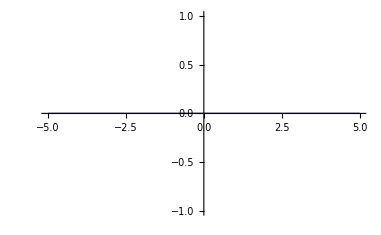

```mathematica
Plot[sigma[e],{e,-5,5}]
```

```mathematica
Simplify[x.U]
```

e